```mathematica
series=Import["/Users/peterkink/hopkins/COVID-19/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
transeries=Transpose[series];
transeries=Drop[transeries,1];
Dimensions[transeries]
hopdates=Drop[series[[1]],4]
%//Length
countriescsv=transeries[[1]];
%//Dimensions
hopdatetodate[dstring_]:=ToExpression["{"<>StringReplace[dstring,"/"->","]<>"}"][[{3,1,2}]]+{2000,0,0}
```

{107,267}

{1/22/20,1/23/20,1/24/20,1/25/20,1/26/20,1/27/20,1/28/20,1/29/20,1/30/20,1/31/20,2/1/20,2/2/20,2/3/20,2/4/20,2/5/20,2/6/20,2/7/20,2/8/20,2/9/20,2/10/20,2/11/20,2/12/20,2/13/20,2/14/20,2/15/20,2/16/20,2/17/20,2/18/20,2/19/20,2/20/20,2/21/20,2/22/20,2/23/20,2/24/20,2/25/20,2/26/20,2/27/20,2/28/20,2/29/20,3/1/20,3/2/20,3/3/20,3/4/20,3/5/20,3/6/20,3/7/20,3/8/20,3/9/20,3/10/20,3/11/20,3/12/20,3/13/20,3/14/20,3/15/20,3/16/20,3/17/20,3/18/20,3/19/20,3/20/20,3/21/20,3/22/20,3/23/20,3/24/20,3/25/20,3/26/20,3/27/20,3/28/20,3/29/20,3/30/20,3/31/20,4/1/20,4/2/20,4/3/20,4/4/20,4/5/20,4/6/20,4/7/20,4/8/20,4/9/20,4/10/20,4/11/20,4/12/20,4/13/20,4/14/20,4/15/20,4/16/20,4/17/20,4/18/20,4/19/20,4/20/20,4/21/20,4/22/20,4/23/20,4/24/20,4/25/20,4/26/20,4/27/20,4/28/20,4/29/20,4/30/20,5/1/20,5/2/20,5/3/20,5/4/20}

104

{267}

```mathematica
TableForm[series];
```

```mathematica
TableForm[s];
```

```mathematica
CountryData["Japan","Population"]
```

126225259

```mathematica
{"Singapore",200,{2.835279843883035*^8,64.38918662693713,0.1259411788554341},21,7,10,0},
```

```mathematica
{"Spain",300,{215675.98160202175,3181.500137016704,0.14826151757050574},28,14,10,0},
```

```mathematica
countryparameters=
(*name,truncdrop,jp0,lag,projtime,bootlag,plotdrop*)
{
{"Spain",300,{215675.98160202175,3181.500137016704,0.14826151757050574},28,21,10,0},
{"Canada",200,{69033.4446817933,1494.6920501191814,0.10921835643196758},21,21,10,0},{"Australia",100,{6642.134484142101,97.01587464464787,0.22607528967238058},21,21,10,0},{"New Zealand",5,{1462.86773322965,16.719153253505446,0.23215241560626731},21,21,10,0},{"Croatia",10,{2080.086933053336,26.9766086897981,0.14814788798275189},21,21,10,5},{"Czechia",10,{7568.774229171533,97.48275161524633,0.14777441672550098},21,21,10,5},{"Sweden",200,{27171.006032500765,565.6930684772811,0.09306601982000183},28,21,10,0},{"Greece",50,{2580.5558304144824,113.92779267513082,0.12813716548803347},28,21,10,0},{"Japan",950,{16216.352964752372,443.2767672706728,0.133761429456781},28,21,8,0},{"Denmark",1100,{10043.639623658764,953.1111036642944,0.10608218238316226},28,21,10,0},{"Russia",300,{193682.81162210088,633.4404113161813,0.14594429761026523},21,21,10,0},{"United Kingdom",200,{199335.39146248746,1450.235887070382,0.12238938898995863},21,14,10,0},
{"Hungary",50,{3365.6444625267736,104.40659882066325,0.11408451894205024},28,14,10,0},
{"France",300,{177276.3912847858,1518.766119969371,0.13797898997605668},28,14,10,0},
{"Singapore",900,{21078.466173566427,299.80354836134035,0.17802870984146776},28,14,5,0}
}
```

{{Spain,300,{215676.,3181.5,0.148262},28,21,10,0},{Canada,200,{69033.4,1494.69,0.109218},21,21,10,0},{Australia,100,{6642.13,97.0159,0.226075},21,21,10,0},{New Zealand,5,{1462.87,16.7192,0.232152},21,21,10,0},{Croatia,10,{2080.09,26.9766,0.148148},21,21,10,5},{Czechia,10,{7568.77,97.4828,0.147774},21,21,10,5},{Sweden,200,{27171.,565.693,0.093066},28,21,10,0},{Greece,50,{2580.56,113.928,0.128137},28,21,10,0},{Japan,950,{16216.4,443.277,0.133761},28,21,8,0},{Denmark,1100,{10043.6,953.111,0.106082},28,21,10,0},{Russia,300,{193683.,633.44,0.145944},21,21,10,0},{United Kingdom,200,{199335.,1450.24,0.122389},21,14,10,0},{Hungary,50,{3365.64,104.407,0.114085},28,14,10,0},{France,300,{177276.,1518.77,0.137979},28,14,10,0},{Singapore,900,{21078.5,299.804,0.178029},28,14,5,0}}

```mathematica
Export["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml",countryparameters]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml

```mathematica
countryparameters=Import["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml"]
```

{{Spain,300,{213912.,3137.49,0.149177},28,21,10,0},{Canada,200,{69033.4,1494.69,0.109218},21,21,10,0},{Australia,100,{6642.13,97.0159,0.226075},21,21,10,0},{New Zealand,5,{1462.87,16.7192,0.232152},21,21,10,0},{Croatia,10,{2080.09,26.9766,0.148148},21,21,10,5},{Czechia,10,{7568.77,97.4828,0.147774},21,21,10,5},{Sweden,200,{27171.,565.693,0.093066},28,21,10,0},{Greece,50,{2580.56,113.928,0.128137},28,21,10,0},{Japan,950,{16216.4,443.277,0.133761},28,21,8,0},{Denmark,1100,{10043.6,953.111,0.106082},28,21,10,0},{Russia,300,{193683.,633.44,0.145944},21,21,10,0},{United Kingdom,200,{199335.,1450.24,0.122389},21,14,10,0}}

```mathematica
"Spain",
```

```mathematica
wolfcountrynames={"Spain","Canada","Australia","New Zealand","Croatia","CzechRepublic","Sweden","Greece","Japan","Denmark","Russia","United Kingdom","Hungary","France","Singapore"};
wpopulations=Map[CountryData[#,"Population"][[1]]&,wolfcountrynames]
lesscountrynames={};
morecountrynames={};
```

{47290504,35309555,23502754,4554858,4369961,10611300,9595619,11470255,126225259,5628958,142400066,63556184,9918377,64101308,5336859}

```mathematica
countrybootabcs={};
lesscountrybootabcs={};
morecountrybootabcs={};
```

```mathematica
SetDirectory["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/plotdump"]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/plotdump

country : Spain

data length : 60

start date : {2020,3,6}

jdp0 : {214499.,3187.08,0.148419}

jp20 : {222455.,7032.75,0.119934}

backward result : {149173.,836.891,0.222881}

forward result : {222455.,7032.75,0.119934}

last tab: {222455.,7032.75,0.119934}

backward result : {149173.,836.891,0.222881}

forward result : {222455.,7032.75,0.119934}

past errors : {{-4544.75,-4459.95,-4116.86,-4153.31,-3222.49,-3797.85,-4782.16,-2520.39,-2431.81,-2600.96},-3663.05}

boot tab : {{199112.,2481.71,0.162498},{199842.,2610.71,0.160321},{199409.,2700.71,0.159134},{205449.,3197.96,0.151168},{217703.,4207.,0.13812},{229984.,5464.96,0.126216},{230782.,6022.49,0.122705},{245899.,8067.76,0.110009},{249949.,9380.5,0.104394},{261269.,11828.9,0.0951872},{275149.,14743.7,0.0863712},{294683.,18469.8,0.0772096},{258764.,15091.6,0.0883006},{259045.,16320.3,0.086001},{254339.,16723.4,0.0862512},{248448.,16607.2,0.08778},{244051.,16445.,0.0891995},{238771.,15493.1,0.0923905},{232287.,13164.6,0.0990825},{225007.,9571.6,0.110741},{222862.,8083.63,0.116231},{218459.,5293.01,0.129732},{219566.,5324.3,0.12881}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60}

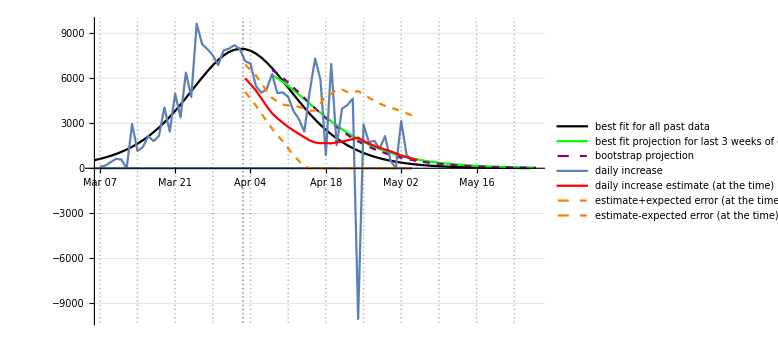

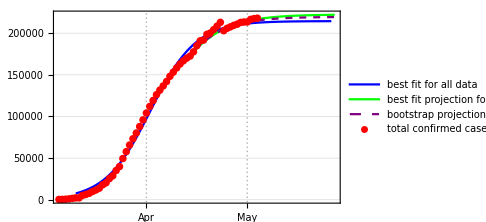

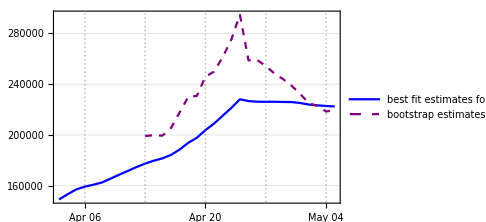

May 04

Spaindate.txt

Spaingraf.png

Spainloggraf.png

Spaindfgraf.png

Spainfinalplot.png

country : Canada

data length : 51

start date : {2020,3,15}

jdp0 : {70900.3,1556.96,0.107065}

jp20 : {86752.5,3019.05,0.0824157}

backward result : {19758.,271.885,0.236761}

forward result : {86752.5,3019.05,0.0824157}

last tab: {86752.5,3019.05,0.0824157}

backward result : {19758.,271.885,0.236761}

forward result : {86752.5,3019.05,0.0824157}

past errors : {{-443.449,-580.441,-775.232,-991.833,-994.63,-1082.45,-833.629,-841.02,196.948,163.27},-618.247}

boot tab : {{45964.5,1055.02,0.134761},{40413.3,945.381,0.143646},{47860.2,1228.25,0.127227},{57820.1,1589.,0.11208},{69248.4,1966.04,0.100292},{78777.9,2323.85,0.0919712},{96797.7,2733.85,0.0835396},{120684.,3157.66,0.0764033},{182039.,3637.78,0.0690106},{230772.,3965.05,0.0651527},{261492.,4221.32,0.0627344},{299529.,4547.98,0.0600505},{209723.,4506.01,0.0616834},{159262.,4447.61,0.0636705},{127431.,4244.93,0.0669304},{112896.,4043.81,0.0697297},{98394.2,3644.62,0.0746826},{91246.,3302.05,0.0788237},{82101.6,2696.91,0.0867844},{85957.5,2949.36,0.0832405},{87589.7,3136.47,0.081158}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51}

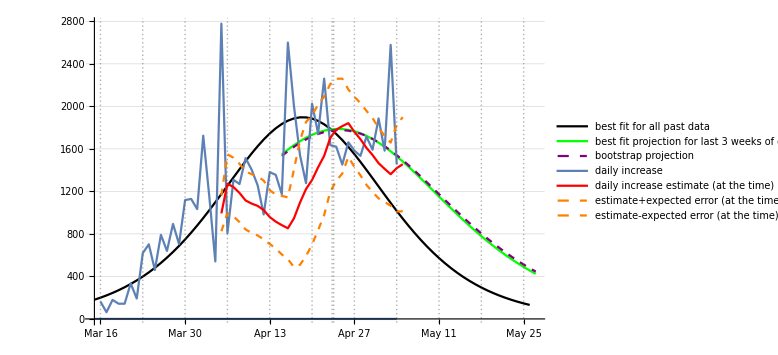

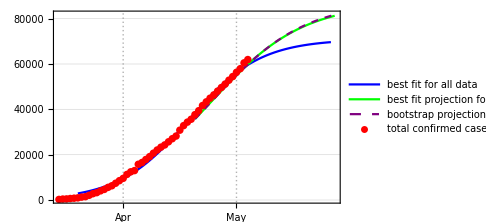

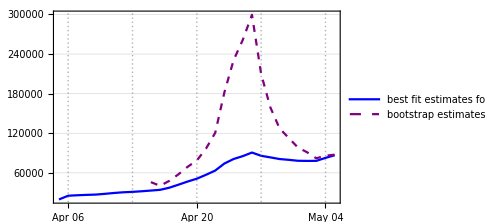

May 04

Canadadate.txt

Canadagraf.png

Canadaloggraf.png

Canadadfgraf.png

Canadafinalplot.png

country : Australia

data length : 56

start date : {2020,3,10}

jdp0 : {6651.99,98.2242,0.225233}

jp20 : {6918.62,2733.7,0.0825573}

backward result : {6333.48,61.3826,0.258068}

forward result : {6918.62,2733.7,0.0825573}

last tab: {6918.62,2733.7,0.0825573}

backward result : {6333.48,61.3826,0.258068}

forward result : {6918.62,2733.7,0.0825573}

past errors : {{5.40561,15.5039,13.8791,29.3692,30.8323,39.1437,46.1945,62.8896,82.1458,103.89},42.9254}

boot tab : {{6236.05,65.0561,0.254921},{6538.97,99.7277,0.227185},{6680.96,127.765,0.212343},{6659.47,126.959,0.213015},{6685.33,145.069,0.206255},{6716.95,169.703,0.198415},{6739.39,206.803,0.189174},{6767.52,252.699,0.179859},{6868.31,385.44,0.159561},{6930.96,513.821,0.14614},{6988.52,689.771,0.132765},{6950.09,730.47,0.131633},{6956.65,930.089,0.122078},{7011.34,1279.75,0.10784},{7030.75,1582.12,0.0988361},{7051.54,1928.15,0.0901406},{7033.47,2055.46,0.0881846},{7051.65,2328.51,0.0823429},{6996.74,2315.34,0.0848807},{7041.47,2891.12,0.0734227},{7032.95,3194.97,0.0691873},{7104.54,3849.32,0.0568132},{7054.82,3814.2,0.0593385},{7026.2,3654.13,0.0628569},{7090.83,4169.7,0.0528867},{7315.92,4992.31,0.0342782}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56}

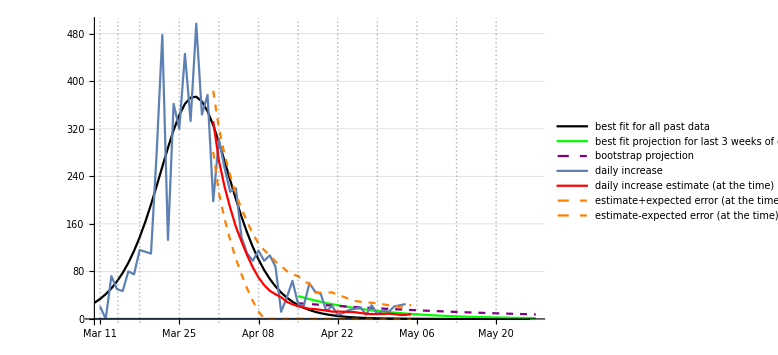

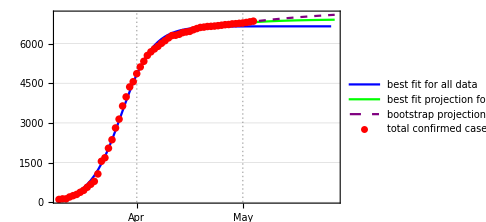

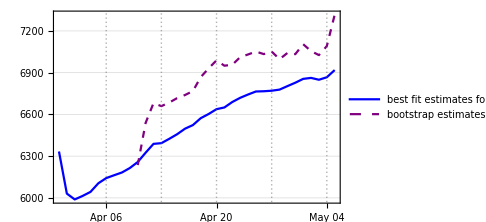

May 04

Australiadate.txt

Australiagraf.png

Australialoggraf.png

Australiadfgraf.png

Australiafinalplot.png

country : New Zealand

data length : 52

start date : {2020,3,14}

jdp0 : {1464.24,16.8451,0.231654}

jp20 : {1494.42,151.552,0.142874}

backward result : {981.19,4.49853,0.341492}

forward result : {1494.42,151.552,0.142874}

last tab: {1494.42,151.552,0.142874}

backward result : {981.19,4.49853,0.341492}

forward result : {1494.42,151.552,0.142874}

past errors : {{15.8974,13.1881,14.7989,15.6706,16.7543,19.0104,24.4066,25.9167,25.5191,24.1966},19.5359}

boot tab : {{1833.01,53.1616,0.158085},{1745.34,52.5281,0.161741},{1653.58,49.0838,0.169019},{1584.85,44.396,0.177548},{1536.2,38.8581,0.18697},{1509.47,34.2446,0.194769},{1500.49,32.6958,0.197606},{1488.29,29.0462,0.2039},{1478.53,26.5983,0.208752},{1482.16,31.3381,0.201653},{1481.68,34.8448,0.197617},{1486.04,47.1765,0.185404},{1494.82,73.9462,0.167186},{1492.82,86.0635,0.162189},{1499.51,118.295,0.149442},{1507.24,167.934,0.135325},{1512.91,217.538,0.124841},{1526.04,352.045,0.104276},{1541.97,501.305,0.0868885},{1541.36,548.281,0.0833017},{1538.38,595.871,0.0804977},{1525.29,553.665,0.0871638}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52}

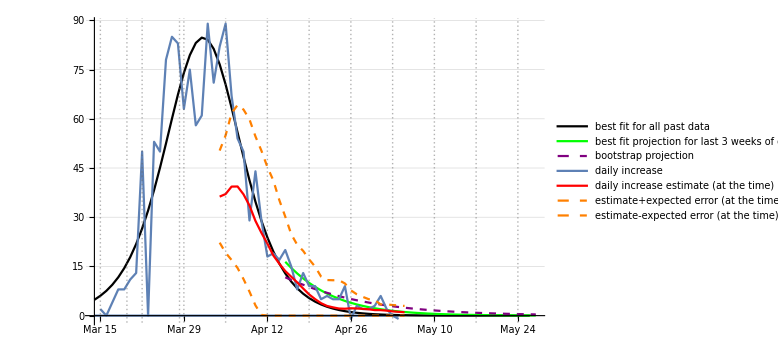

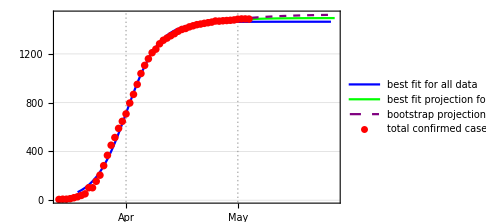

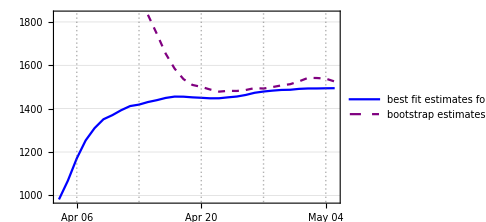

May 04

newzealanddate.txt

newzealandgraf.png

newzealandloggraf.png

newzealanddfgraf.png

newzealandfinalplot.png

country : Croatia

data length : 60

start date : {2020,3,6}

jdp0 : {2084.57,27.3034,0.147586}

jp20 : {2170.07,89.0626,0.111009}

backward result : {835.937,1.62704,0.316962}

forward result : {2170.07,89.0626,0.111009}

last tab: {2170.07,89.0626,0.111009}

backward result : {835.937,1.62704,0.316962}

forward result : {2170.07,89.0626,0.111009}

past errors : {{5.48963,3.97373,-0.934048,-5.38039,-1.50287,2.57045,2.72115,-2.15965,-1.17156,-2.40533},0.120112}

boot tab : {{1753.63,15.3017,0.178544},{1699.93,15.2697,0.179765},{1759.03,17.9074,0.171919},{1918.37,24.168,0.156701},{2031.8,30.4091,0.145864},{2234.16,41.1379,0.131574},{2212.36,46.4471,0.12736},{2419.65,61.3622,0.114706},{2598.91,77.5604,0.104611},{2869.15,98.1151,0.0943032},{3065.29,117.977,0.0868374},{3424.2,144.853,0.0782348},{3431.63,159.817,0.0751471},{3255.65,166.798,0.0748764},{3196.99,179.479,0.0731036},{2820.71,167.394,0.0783883},{2641.69,157.695,0.0823438},{2493.49,137.335,0.0886636},{2381.1,117.462,0.0953606},{2286.,92.5786,0.104378},{2191.95,63.4271,0.117748},{2120.17,38.0182,0.134455},{2098.87,30.1953,0.141603},{2101.61,30.1679,0.141487},{2105.82,31.8647,0.139904},{2134.04,47.6841,0.128203},{2148.14,54.2981,0.124117},{2158.12,67.226,0.11841},{2161.38,73.0866,0.116233},{2160.75,76.2726,0.115303}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60}

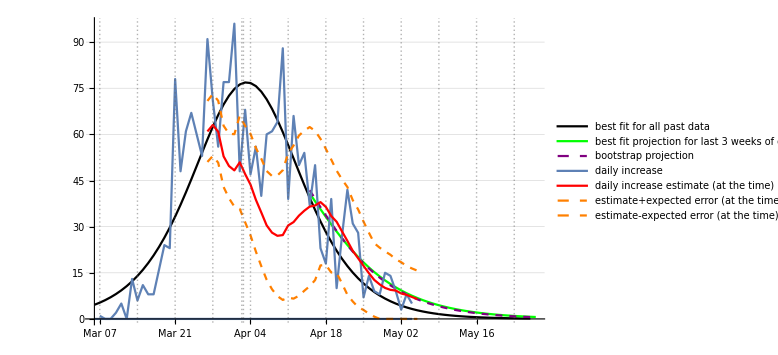

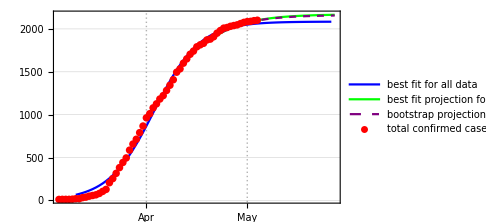

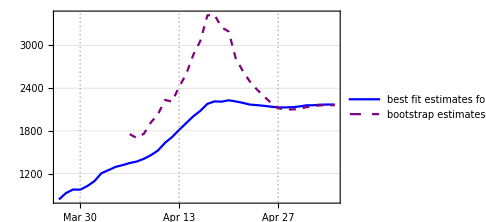

May 04

Croatiadate.txt

Croatiagraf.png

Croatialoggraf.png

Croatiadfgraf.png

Croatiafinalplot.png

country : Czechia

data length : 61

start date : {2020,3,5}

jdp0 : {7601.77,100.082,0.146572}

jp20 : {8189.15,389.123,0.0992758}

backward result : {2216.85,9.55805,0.303903}

forward result : {8189.15,389.123,0.0992758}

last tab: {8189.15,389.123,0.0992758}

backward result : {2216.85,9.55805,0.303903}

forward result : {8189.15,389.123,0.0992758}

past errors : {{59.4597,50.4425,35.3443,42.8411,70.6174,130.369,145.804,127.644,120.627,128.504},91.1653}

boot tab : {{9746.37,89.0792,0.147415},{8757.52,93.6428,0.147021},{7322.81,77.909,0.158933},{6079.92,47.0909,0.186442},{6848.02,73.7599,0.16362},{7931.86,112.511,0.142321},{8162.42,128.142,0.136611},{8321.56,143.242,0.131976},{8165.76,146.739,0.131839},{7956.08,149.669,0.132238},{7426.67,128.353,0.140741},{7457.47,143.195,0.137005},{7719.14,184.128,0.127089},{7803.91,208.119,0.122653},{7528.09,173.829,0.130412},{7492.7,175.735,0.130394},{7657.59,229.587,0.120863},{7980.6,340.932,0.106464},{8354.69,521.848,0.0914293},{8663.22,700.572,0.0810726},{9307.2,1016.19,0.0671598},{9728.51,1209.91,0.0604686},{10030.2,1438.86,0.0545394},{10339.,1677.93,0.0492557},{11487.9,2098.19,0.0400292},{12086.1,2318.22,0.0361193},{11819.,2344.34,0.0363221},{10691.9,2147.86,0.0414476},{9429.07,1653.71,0.0535902},{8767.66,1091.38,0.0686605},{8397.53,646.575,0.0848627}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61}

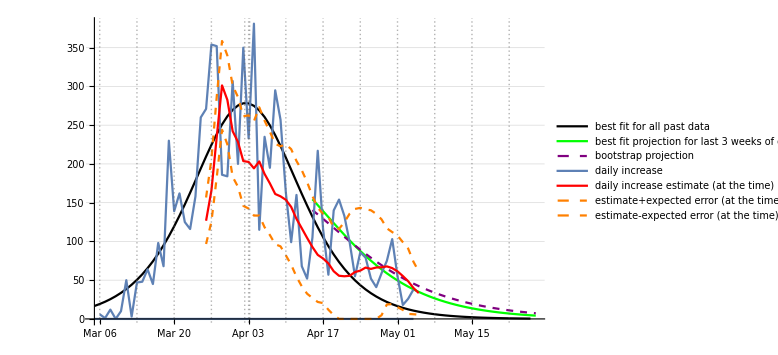

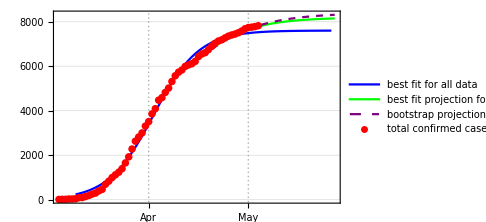

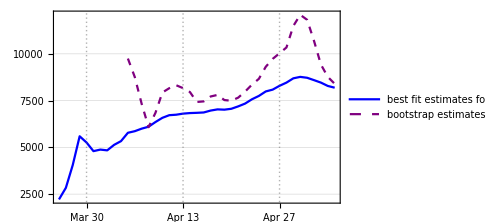

May 04

Czechiadate.txt

Czechiagraf.png

Czechialoggraf.png

Czechiadfgraf.png

Czechiafinalplot.png

country : Sweden

data length : 58

start date : {2020,3,8}

jdp0 : {27374.8,571.743,0.092586}

jp20 : {32641.2,1052.17,0.0735269}

backward result : {33816.,391.165,0.107741}

forward result : {32641.2,1052.17,0.0735269}

last tab: {32641.2,1052.17,0.0735269}

backward result : {33816.,391.165,0.107741}

forward result : {32641.2,1052.17,0.0735269}

past errors : {{632.49,647.648,506.852,796.509,1093.8,1521.68,1608.94,1851.19,1786.92,1911.48},1235.75}

boot tab : {{14328.6,230.525,0.14094},{15189.8,252.891,0.1354},{16812.4,298.978,0.126058},{18482.6,343.08,0.118537},{18921.5,352.548,0.116978},{18681.,340.621,0.118503},{18698.9,343.557,0.118173},{19793.6,391.331,0.112252},{22360.6,500.522,0.101305},{25768.5,630.977,0.0912165},{30601.6,789.143,0.081737},{35234.9,926.372,0.0752642},{38271.4,1035.56,0.071228},{37837.5,1089.33,0.0700247},{40186.1,1191.01,0.0670223},{42912.6,1301.13,0.0640638},{48101.9,1437.3,0.060466},{47961.8,1484.1,0.0597095},{48083.6,1540.1,0.0588103},{42991.7,1484.04,0.0609178},{38885.9,1401.71,0.0636298}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58}

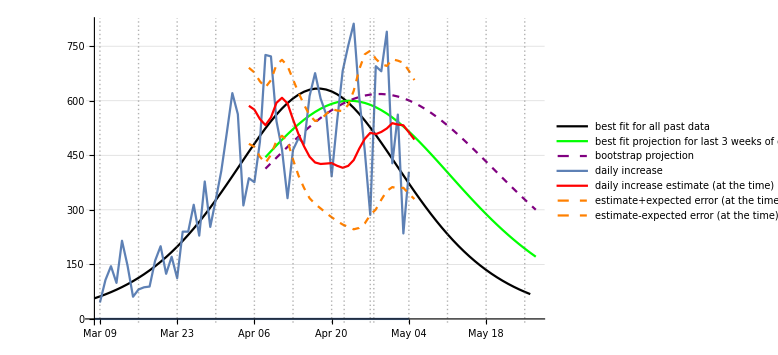

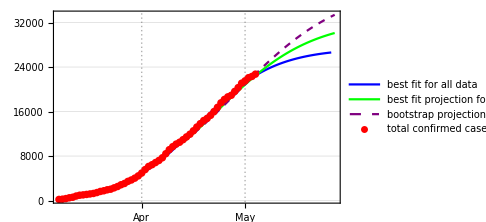

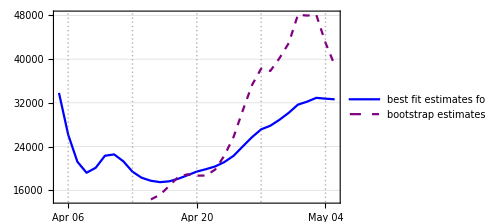

May 04

Swedendate.txt

Swedengraf.png

Swedenloggraf.png

Swedendfgraf.png

Swedenfinalplot.png

country : Greece

data length : 58

start date : {2020,3,8}

jdp0 : {2589.47,115.417,0.127307}

jp20 : {2929.5,580.129,0.0633518}

backward result : {2478.4,89.1455,0.143581}

forward result : {2929.5,580.129,0.0633518}

last tab: {2929.5,580.129,0.0633518}

backward result : {2478.4,89.1455,0.143581}

forward result : {2929.5,580.129,0.0633518}

past errors : {{95.5867,96.4425,104.44,128.458,131.387,140.127,155.589,158.692,160.364,162.541},133.363}

boot tab : {{2352.44,85.4084,0.14789},{2343.2,82.2574,0.149785},{2378.88,87.4267,0.14601},{2379.53,86.5441,0.146415},{2374.13,85.708,0.147053},{2332.45,75.2657,0.15395},{2313.2,68.0001,0.158783},{2460.69,105.336,0.135574},{2480.71,114.594,0.131611},{2574.66,155.517,0.116975},{2663.68,207.482,0.103821},{2751.31,268.599,0.0923139},{2831.38,333.203,0.0829139},{2981.54,446.152,0.0698082},{3254.89,597.533,0.0555793},{3545.4,723.148,0.0460135},{3813.47,804.55,0.0403635},{3858.77,851.617,0.0382303},{3782.99,876.723,0.0378806},{3567.73,866.674,0.0401119},{3425.27,878.147,0.0412799}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58}

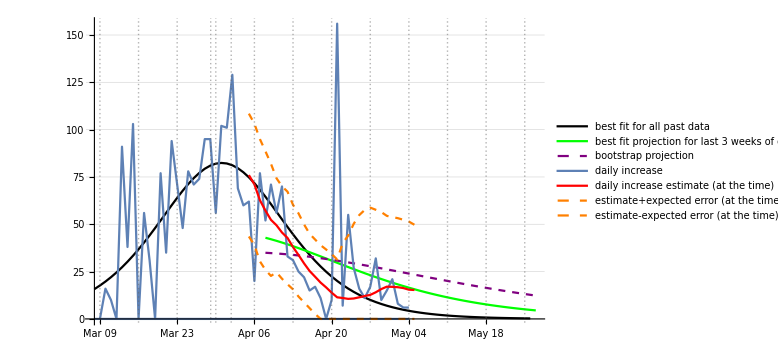

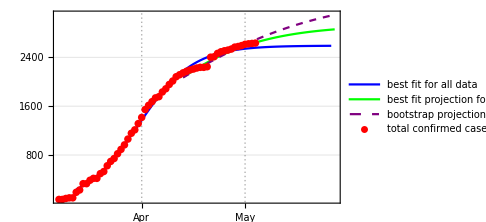

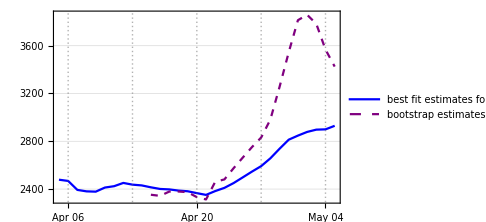

May 04

Greecedate.txt

Greecegraf.png

Greeceloggraf.png

Greecedfgraf.png

Greecefinalplot.png

country : Japan

data length : 46

start date : {2020,3,20}

jdp0 : {16217.2,443.334,0.133754}

jp20 : {15604.6,293.131,0.151172}

backward result : {61680.7,682.989,0.0970644}

forward result : {15604.6,293.131,0.151172}

last tab: {15604.6,293.131,0.151172}

backward result : {61680.7,682.989,0.0970644}

forward result : {15604.6,293.131,0.151172}

past errors : {{391.75,-306.53,-401.7,-437.372,-425.297,-342.296,-199.201,-142.814},-232.933}

boot tab : {{13315.9,224.523,0.172372},{12884.9,183.951,0.183025},{12913.8,169.381,0.18627},{13895.7,210.611,0.172145},{14183.,221.253,0.168669},{14778.9,252.027,0.160776},{15213.8,273.627,0.155685},{15185.2,264.216,0.157101},{15204.2,253.168,0.158499},{15385.7,269.733,0.155293},{15572.8,286.889,0.152121}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46}

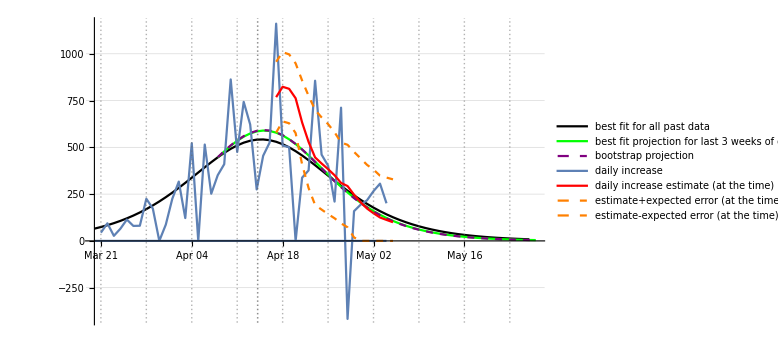

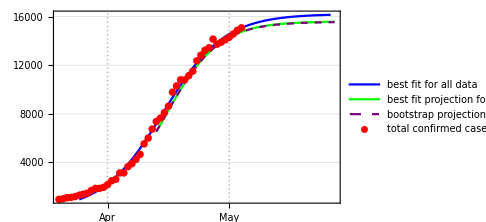

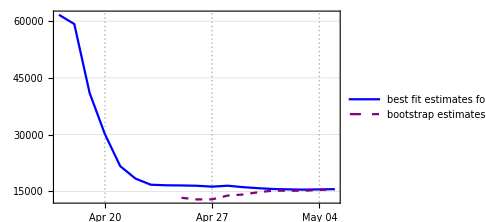

May 04

Japandate.txt

Japangraf.png

Japanloggraf.png

Japandfgraf.png

Japanfinalplot.png

country : Denmark

data length : 48

start date : {2020,3,18}

jdp0 : {10139.8,967.387,0.104663}

jp20 : {12443.9,2255.39,0.0593257}

backward result : {9622.11,847.804,0.116597}

forward result : {12443.9,2255.39,0.0593257}

last tab: {12443.9,2255.39,0.0593257}

backward result : {9622.11,847.804,0.116597}

forward result : {12443.9,2255.39,0.0593257}

past errors : {{381.545,446.051,510.792,612.059,723.192,832.582,949.67,1013.95,1101.95,1224.26},779.605}

boot tab : {{8789.2,690.271,0.132732},{9408.77,861.385,0.115934},{9904.5,1019.76,0.104163},{10433.3,1208.42,0.0930967},{11116.9,1440.04,0.0818724},{12051.9,1723.91,0.0705372},{13311.5,2038.43,0.0600674},{14942.3,2343.1,0.0513308},{16294.8,2588.,0.0456477},{18136.9,2839.26,0.0403361},{21170.9,3096.81,0.035147}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48}

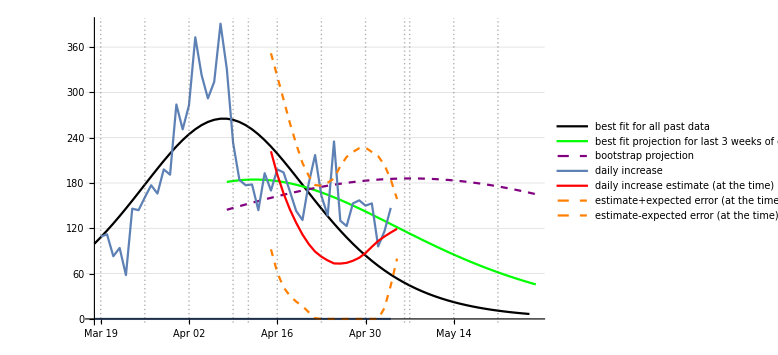

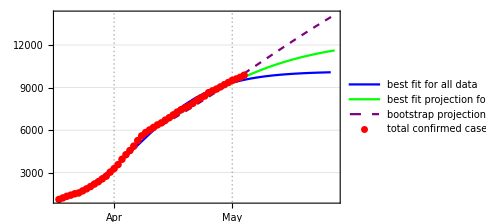

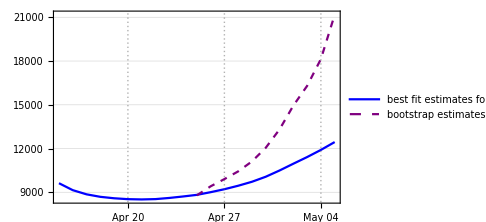

May 04

Denmarkdate.txt

Denmarkgraf.png

Denmarkloggraf.png

Denmarkdfgraf.png

Denmarkfinalplot.png

country : Russia

data length : 45

start date : {2020,3,21}

jdp0 : {216620.,744.609,0.139272}

jp20 : {268499.,1277.8,0.121216}

backward result : {40899.,291.658,0.19182}

forward result : {268499.,1277.8,0.121216}

last tab: {268499.,1277.8,0.121216}

backward result : {40899.,291.658,0.19182}

forward result : {268499.,1277.8,0.121216}

past errors : {{182.417,1165.,2209.15,3750.36,5050.65,7967.87,12093.3,18285.4,25855.6,33725.3},11028.5}

boot tab : {{339753.,540.719,0.148964},{272232.,541.224,0.149824},{216291.,537.8,0.151313},{166931.,488.092,0.156903},{148516.,426.755,0.163075},{133704.,340.318,0.172608},{134487.,325.5,0.174075},{134147.,304.939,0.176344},{130117.,251.508,0.183418},{113530.,111.805,0.213888},{132929.,236.39,0.184824},{153795.,406.755,0.164158},{195097.,798.069,0.139122},{277844.,1473.14,0.116604},{402294.,2168.37,0.102661}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}

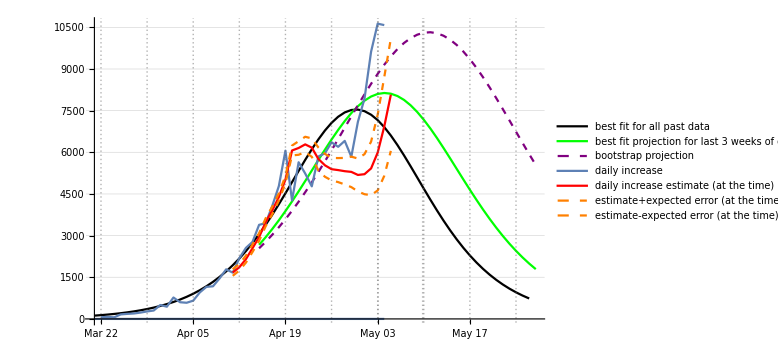

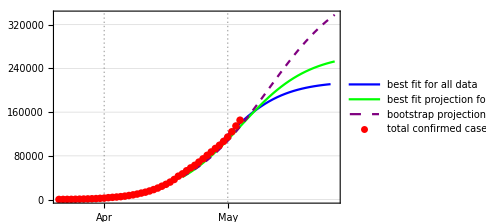

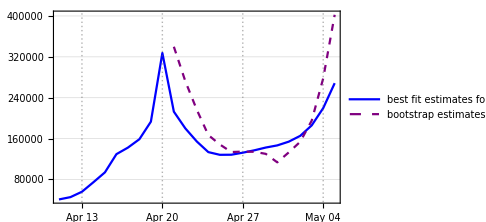

May 04

Russiadate.txt

Russiagraf.png

Russialoggraf.png

Russiadfgraf.png

Russiafinalplot.png

country : United Kingdom

data length : 59

start date : {2020,3,7}

jdp0 : {203578.,1549.12,0.119975}

jp20 : {277366.,8602.43,0.0718861}

backward result : {109233.,204.099,0.209633}

forward result : {277366.,8602.43,0.0718861}

last tab: {277366.,8602.43,0.0718861}

backward result : {109233.,204.099,0.209633}

forward result : {277366.,8602.43,0.0718861}

past errors : {{2895.28,4014.6,5233.67,6392.72,7879.71,11542.9,15584.6,18437.9,21005.2,23393.3},11638.}

boot tab : {{83241.9,195.501,0.211712},{78715.9,169.211,0.218966},{104119.,386.441,0.179579},{124173.,562.919,0.162089},{161690.,722.568,0.149431},{167872.,807.496,0.145055},{167177.,860.08,0.143001},{161292.,887.738,0.142526},{173543.,1053.12,0.13579},{164724.,1037.13,0.137269},{173159.,1212.29,0.131495},{191688.,1498.9,0.123273},{201406.,1708.79,0.1186},{216532.,2016.16,0.112684},{204744.,2024.87,0.113565},{199855.,2112.68,0.112913},{199191.,2256.34,0.111236},{206738.,2631.07,0.106331},{218142.,3158.27,0.100419},{233208.,3921.28,0.0935452},{245292.,4596.52,0.0886055},{256027.,5373.87,0.0839984},{266253.,6354.42,0.0792965},{271707.,7244.,0.0758797},{303860.,9479.33,0.0678445},{342853.,11586.,0.0616172},{384735.,13746.,0.0564606},{420258.,15595.3,0.0528094},{442573.,17236.6,0.0501939}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59}

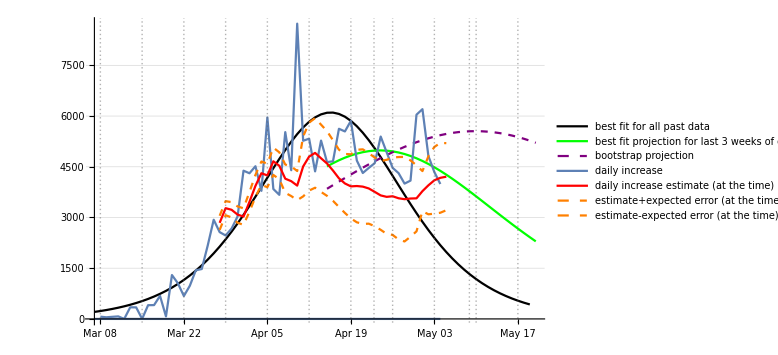

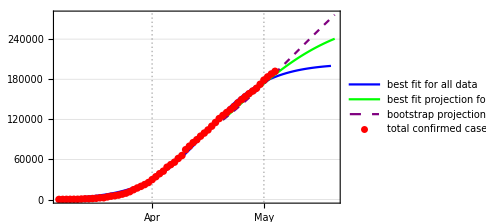

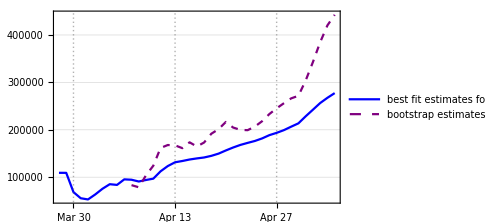

May 04

ukdate.txt

ukgraf.png

ukloggraf.png

ukdfgraf.png

ukfinalplot.png

country : Hungary

data length : 48

start date : {2020,3,18}

jdp0 : {3393.19,105.833,0.113257}

jp20 : {3548.72,134.462,0.103556}

backward result : {3559.03,90.161,0.121211}

forward result : {3548.72,134.462,0.103556}

last tab: {3548.72,134.462,0.103556}

backward result : {3559.03,90.161,0.121211}

forward result : {3548.72,134.462,0.103556}

past errors : {{11.6642,1.00762,20.4562,27.0302,49.6963,46.3751,86.9493,122.271,138.169,138.455},64.2073}

boot tab : {{3044.96,96.0426,0.121224},{3174.56,105.671,0.115803},{3330.85,114.155,0.111136},{3420.45,118.838,0.108739},{3501.07,123.761,0.106464},{3623.3,132.405,0.102939},{3679.16,137.508,0.101118},{3775.03,146.665,0.0981112},{3908.22,160.356,0.0940671},{3912.03,166.408,0.0928646},{3757.9,161.808,0.0952574}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48}

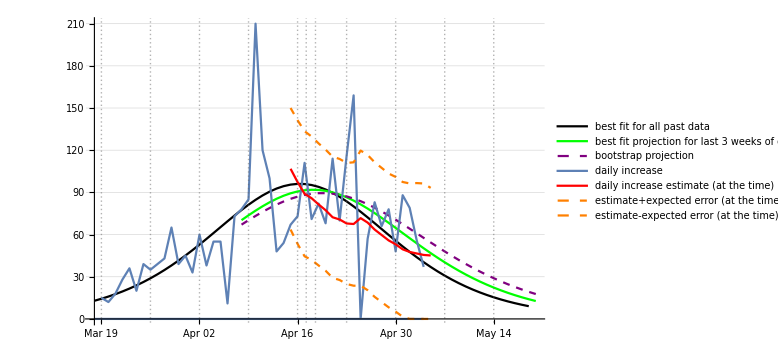

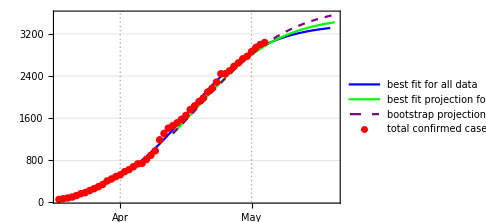

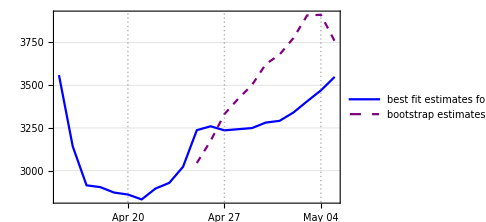

May 04

Hungarydate.txt

Hungarygraf.png

Hungaryloggraf.png

Hungarydfgraf.png

Hungaryfinalplot.png

country : France

data length : 61

start date : {2020,3,5}

jdp0 : {176816.,1499.5,0.138481}

jp20 : {168958.,109.858,0.207445}

backward result : {113682.,799.423,0.176917}

forward result : {168958.,109.858,0.207445}

last tab: {168958.,109.858,0.207445}

backward result : {113682.,799.423,0.176917}

forward result : {168958.,109.858,0.207445}

past errors : {{-7853.96,-9743.15,-8241.65,-7183.98,-11531.9,-12434.2,-13921.2,-14050.,-14846.6,-15266.8},-11507.4}

boot tab : {{106792.,853.645,0.175194},{201833.,2616.02,0.11642},{294439.,3813.15,0.0985153},{440984.,4843.79,0.0874727},{535015.,5397.82,0.0829994},{887709.,5847.48,0.0788206},{824902.,6165.43,0.0774565},{575923.,6119.55,0.0791565},{489370.,6013.28,0.0807104},{410677.,5810.09,0.083058},{364632.,5587.52,0.0853636},{247538.,4071.31,0.099892},{195876.,2259.24,0.12284},{172293.,1176.87,0.14666},{164753.,788.875,0.160283},{152737.,373.292,0.186111},{152267.,292.094,0.193025},{156296.,279.592,0.191939},{154939.,173.258,0.20524},{156413.,131.991,0.211361},{157158.,85.9456,0.221847},{160019.,67.6592,0.225927},{161798.,49.6329,0.232403},{163385.,35.6734,0.239374}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61}

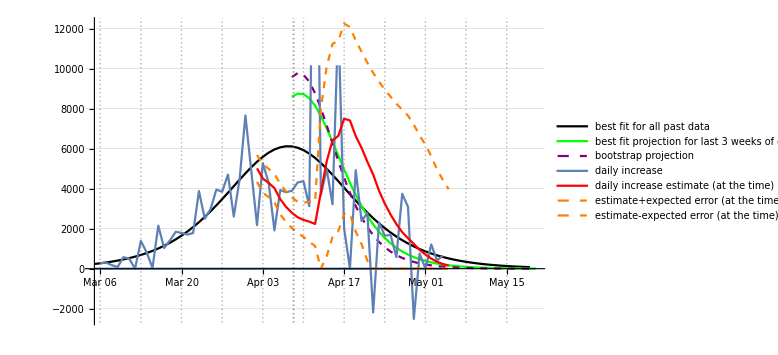

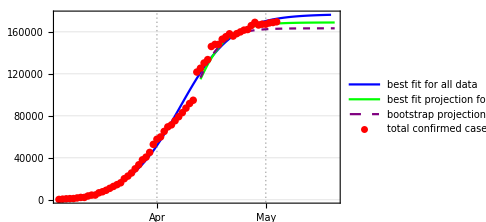

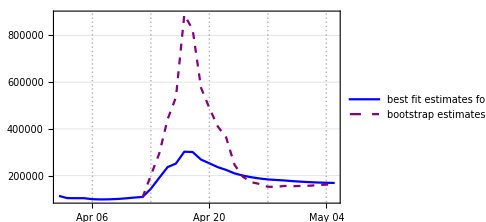

May 04

Francedate.txt

Francegraf.png

Franceloggraf.png

Francedfgraf.png

Francefinalplot.png

country : Singapore

data length : 35

start date : {2020,3,31}

jdp0 : {21239.6,305.422,0.176812}

jp20 : {20657.6,251.609,0.186742}

backward result : {25787.1,368.544,0.161986}

forward result : {20657.6,251.609,0.186742}

last tab: {20657.6,251.609,0.186742}

backward result : {25787.1,368.544,0.161986}

forward result : {20657.6,251.609,0.186742}

past errors : {{-475.533,-169.524,-283.701,-125.091,8.94383},-208.981}

boot tab : {{18609.7,185.163,0.206979},{19843.4,225.079,0.194109},{20798.2,259.355,0.184972}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35}

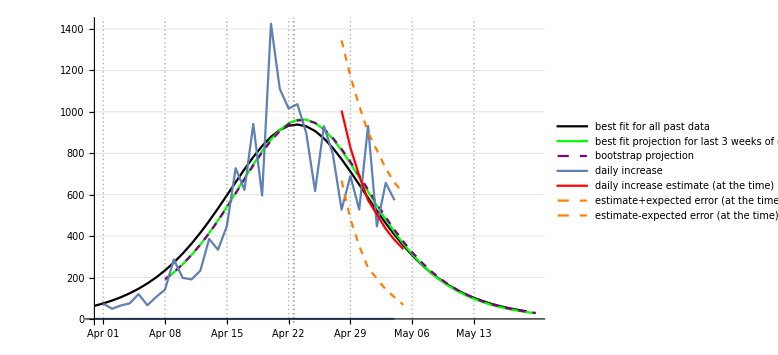

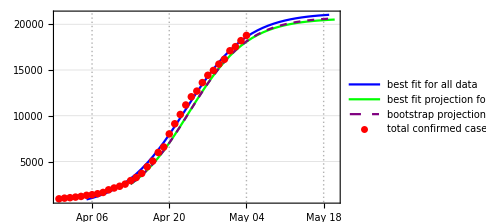

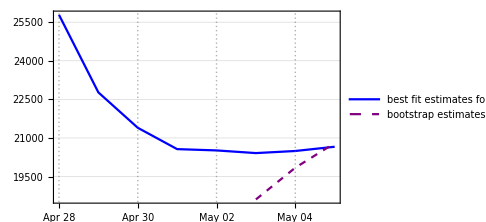

May 04

Singaporedate.txt

Singaporegraf.png

Singaporeloggraf.png

Singaporedfgraf.png

Singaporefinalplot.png

{88.51728,Null}

```mathematica
countrydateplotlist={};
Timing[
For[cit=1,cit≤Length[countryparameters],cit++,
countrynames=Transpose[countryparameters][[1]];
currentnamme=countrynames[[cit]];
{currentnamme,ctrunc,jdp0,jlag,jprojtime,jbootlag,jplotdrop}=countryparameters[[cit]];
Print["country : ",currentnamme];
countinds=Flatten[Position[countriescsv,currentnamme]];
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}];

truncdatesandata=Select[datesanddata,#[[2]]>ctrunc&];
justdata=Transpose[truncdatesandata][[2]];
justtime=Table[i,{i,Length[justdata]}];
(*jstartdate=truncdatesandata[[1,1]]-{0,0,1}*)
jstartdate=truncdatesandata[[1,1]];
Print["data length : ",Length[justdata]];
Print["start date : ",jstartdate];

{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime];
Print["jdp0 : ",jdp0];
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,jlag,justtime,{1,0}];
Print["jp20 : ",jp20];

(*update jdp0*)
countryparameters[[cit,3]]=jdp0;

{jgraf,jloggraf,jdfpplot,jprogplot,jfinal,jbootabc}=somegraphs2[jdp0,jp20,justtime,justdata,jstartdate,jlag,jprojtime,5,jbootlag,wpopulations[[cit]]];
jdatestring=reldatetostring[jstartdate,justtime[[-1]]-1];
Print[jgraf];
Print[jloggraf];
Print[jfinal];

(*jdatestring=reldatetostring[cpstartdate,timecpert[[-1]]];*)

Print[jdatestring];

If[jp20[[1]]10^5/wpopulations[[cit]]>grafthreshhold,
morecountrynames=AppendTo[morecountrynames,currentnamme],
lesscountrynames=AppendTo[lesscountrynames,currentnamme]
];

(*new zealand string exception*)
If[currentnamme==="New Zealand",currentnamme="newzealand"];
(*uk  string exception*)
If[currentnamme==="United Kingdom",currentnamme="uk"];


datefilename=currentnamme<>"date.txt";
Print[datefilename];
Export[datefilename,jdatestring];
graffilename=currentnamme<>"graf.png";
Export[graffilename,jgraf];
Print[graffilename];
loggraffilename=currentnamme<>"loggraf.png";
Export[loggraffilename,jloggraf];
Print[loggraffilename];
dfgraffilename=currentnamme<>"dfgraf.png";
Export[dfgraffilename,jdfpplot];
Print[dfgraffilename];
finalgraffilename=currentnamme<>"finalplot.png";
Export[finalgraffilename,jfinal];
Print[finalgraffilename];

drcases=Transpose[datesanddata][[2]];
drcases=drcases/wpopulations[[cit]];
datesanddata=Transpose[{Transpose[datesanddata][[1]],drcases}];
countrydateplotlist=AppendTo[countrydateplotlist,datesanddata];
]
]
```

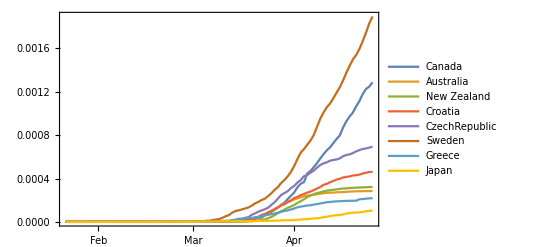

```mathematica
DateListPlot[countrydateplotlist,PlotLegends->wolfcountrynames,PlotRange->All]
```

```mathematica
allcountrynames=Join[fwcountrynames,wolfcountrynames]
%//Length
Length[countrybootabcs]
```

{Slovenia,Italy,Austria,Germany,USA,Canada,Australia,New Zealand,Croatia,CzechRepublic,Singapore,Japan}

12

12

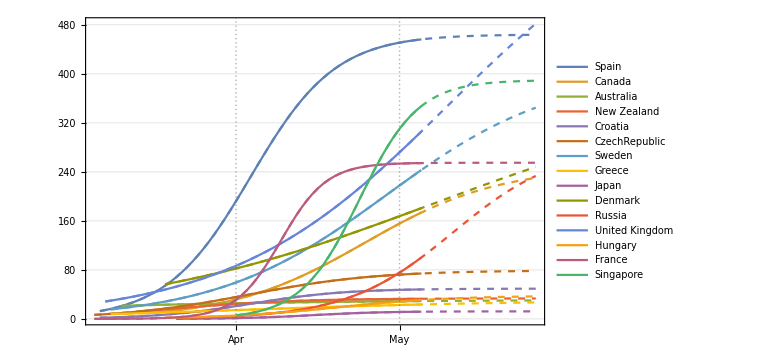

```mathematica
projfwcountryplot=DateListPlot[countrybootabcs,PlotRange->All,ImageSize->Large,PlotTheme->"Detailed",PlotStyle->Dashed];
trunccountrybootabcs=Map[Drop[#,-grafprojtime]&,countrybootabcs];
pastfwcountryplot=DateListPlot[trunccountrybootabcs,PlotRange->All,PlotLegends->wolfcountrynames,ImageSize->Large,PlotTheme->"Detailed"];
mscprojplots=Show[projfwcountryplot,pastfwcountryplot,ImageSize->Large]
```

```mathematica
Export["mscprojplots.png",mscprojplots]
```

mscprojplots.png

```mathematica
countrybootabcs//Length
morecountrybootabcs//Length
lesscountrybootabcs//Length
morecountrynames
lesscountrynames
```

15

8

7

{Spain,Canada,Sweden,Denmark,Russia,United Kingdom,France,Singapore}

{Australia,New Zealand,Croatia,Czechia,Greece,Japan,Hungary}

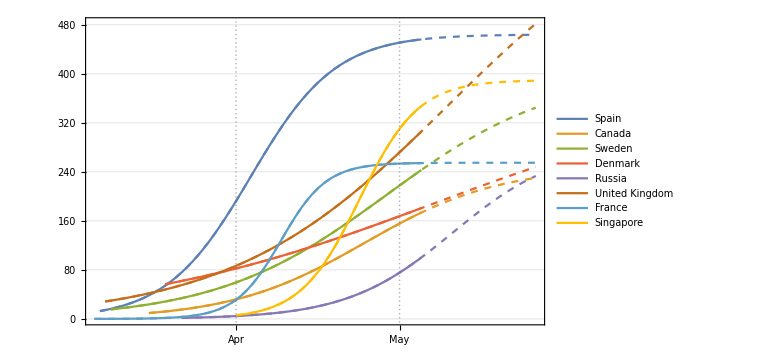

```mathematica
projfwcountryplot=DateListPlot[morecountrybootabcs,PlotRange->All,ImageSize->Large,PlotTheme->"Detailed",PlotStyle->Dashed];
trunccountrybootabcs=Map[Drop[#,-grafprojtime]&,morecountrybootabcs];
pastfwcountryplot=DateListPlot[trunccountrybootabcs,PlotRange->All,PlotLegends->morecountrynames,ImageSize->Large,PlotTheme->"Detailed"];
mscprojplots=Show[projfwcountryplot,pastfwcountryplot,ImageSize->Large]
```

```mathematica
Export["moremscprojplots.png",mscprojplots]
```

moremscprojplots.png

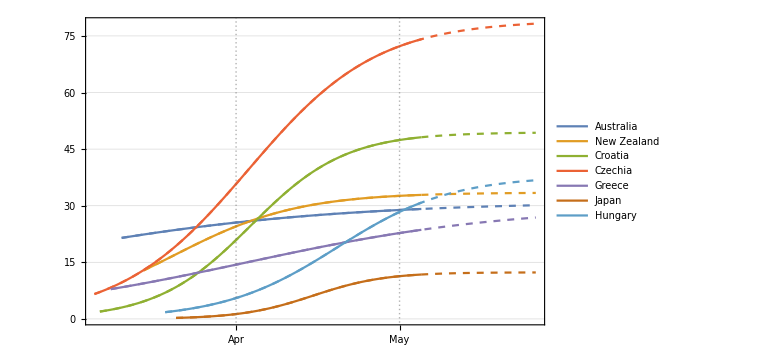

```mathematica
projfwcountryplot=DateListPlot[lesscountrybootabcs,PlotRange->All,ImageSize->Large,PlotTheme->"Detailed",PlotStyle->Dashed];
trunccountrybootabcs=Map[Drop[#,-grafprojtime]&,lesscountrybootabcs];
pastfwcountryplot=DateListPlot[trunccountrybootabcs,PlotRange->All,PlotLegends->lesscountrynames,ImageSize->Large,PlotTheme->"Detailed"];
mscprojplots=Show[projfwcountryplot,pastfwcountryplot,ImageSize->Large]
```

```mathematica
Export["lessmscprojplots.png",mscprojplots]
```

lessmscprojplots.png

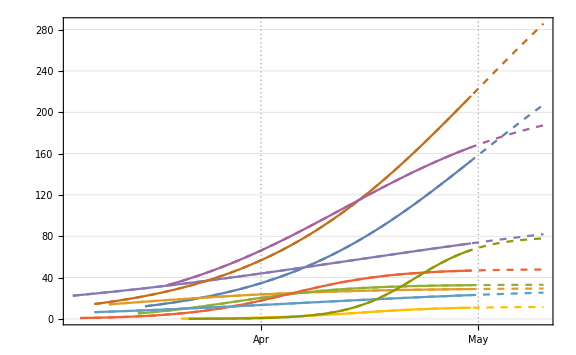
```mathematica
29.4.
-Graphics-
```

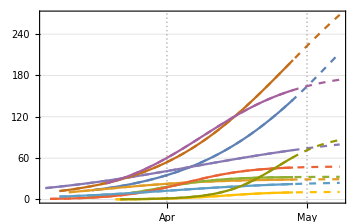
```mathematica
28.4.
-Graphics-
```

```mathematica
Export["mscprojplots.png",mscprojplots]
```

mscprojplots.png

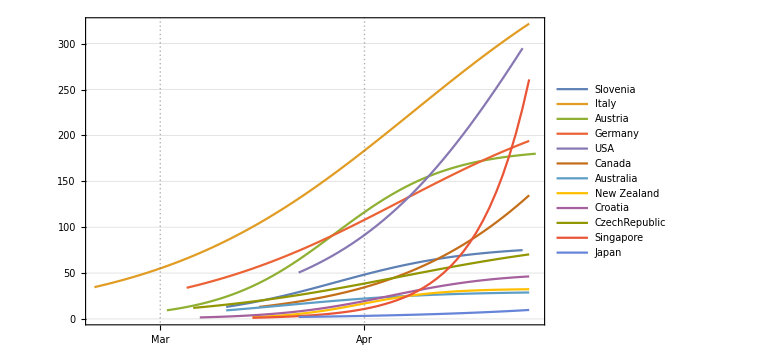

```mathematica
DateListPlot[countrybootabcs,PlotRange->All,PlotLegends->allcountrynames,ImageSize->Large,PlotTheme->"Detailed"]
```

```mathematica
ColorData
```

```mathematica
countinds=Flatten[Position[countriescsv,"Singapore"]]
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}]
```

{198}

{{{2020,1,22},0},{{2020,1,23},1},{{2020,1,24},3},{{2020,1,25},3},{{2020,1,26},4},{{2020,1,27},5},{{2020,1,28},7},{{2020,1,29},7},{{2020,1,30},10},{{2020,1,31},13},{{2020,2,1},16},{{2020,2,2},18},{{2020,2,3},18},{{2020,2,4},24},{{2020,2,5},28},{{2020,2,6},28},{{2020,2,7},30},{{2020,2,8},33},{{2020,2,9},40},{{2020,2,10},45},{{2020,2,11},47},{{2020,2,12},50},{{2020,2,13},58},{{2020,2,14},67},{{2020,2,15},72},{{2020,2,16},75},{{2020,2,17},77},{{2020,2,18},81},{{2020,2,19},84},{{2020,2,20},84},{{2020,2,21},85},{{2020,2,22},85},{{2020,2,23},89},{{2020,2,24},89},{{2020,2,25},91},{{2020,2,26},93},{{2020,2,27},93},{{2020,2,28},93},{{2020,2,29},102},{{2020,3,1},106},{{2020,3,2},108},{{2020,3,3},110},{{2020,3,4},110},{{2020,3,5},117},{{2020,3,6},130},{{2020,3,7},138},{{2020,3,8},150},{{2020,3,9},150},{{2020,3,10},160},{{2020,3,11},178},{{2020,3,12},178},{{2020,3,13},200},{{2020,3,14},212},{{2020,3,15},226},{{2020,3,16},243},{{2020,3,17},266},{{2020,3,18},313},{{2020,3,19},345},{{2020,3,20},385},{{2020,3,21},432},{{2020,3,22},455},{{2020,3,23},509},{{2020,3,24},558},{{2020,3,25},631},{{2020,3,26},683},{{2020,3,27},732},{{2020,3,28},802},{{2020,3,29},844},{{2020,3,30},879},{{2020,3,31},926},{{2020,4,1},1000},{{2020,4,2},1049},{{2020,4,3},1114},{{2020,4,4},1189},{{2020,4,5},1309},{{2020,4,6},1375},{{2020,4,7},1481},{{2020,4,8},1623},{{2020,4,9},1910},{{2020,4,10},2108},{{2020,4,11},2299},{{2020,4,12},2532},{{2020,4,13},2918},{{2020,4,14},3252},{{2020,4,15},3699},{{2020,4,16},4427},{{2020,4,17},5050},{{2020,4,18},5992},{{2020,4,19},6588},{{2020,4,20},8014},{{2020,4,21},9125},{{2020,4,22},10141},{{2020,4,23},11178},{{2020,4,24},12075},{{2020,4,25},12693},{{2020,4,26},13624},{{2020,4,27},14423},{{2020,4,28},14951},{{2020,4,29},15641},{{2020,4,30},16169},{{2020,5,1},17101},{{2020,5,2},17548},{{2020,5,3},18205}}

```mathematica
truncdatesandata=Select[datesanddata,#[[2]]>900&]
%//Length
justdata=Transpose[truncdatesandata][[2]]
justtime=Table[i,{i,Length[justdata]}];
(*jstartdate=truncdatesandata[[1,1]]-{0,0,1}*)
jstartdate=truncdatesandata[[1,1]]
```

{{{2020,3,31},926},{{2020,4,1},1000},{{2020,4,2},1049},{{2020,4,3},1114},{{2020,4,4},1189},{{2020,4,5},1309},{{2020,4,6},1375},{{2020,4,7},1481},{{2020,4,8},1623},{{2020,4,9},1910},{{2020,4,10},2108},{{2020,4,11},2299},{{2020,4,12},2532},{{2020,4,13},2918},{{2020,4,14},3252},{{2020,4,15},3699},{{2020,4,16},4427},{{2020,4,17},5050},{{2020,4,18},5992},{{2020,4,19},6588},{{2020,4,20},8014},{{2020,4,21},9125},{{2020,4,22},10141},{{2020,4,23},11178},{{2020,4,24},12075},{{2020,4,25},12693},{{2020,4,26},13624},{{2020,4,27},14423},{{2020,4,28},14951},{{2020,4,29},15641},{{2020,4,30},16169},{{2020,5,1},17101},{{2020,5,2},17548},{{2020,5,3},18205}}

34

{926,1000,1049,1114,1189,1309,1375,1481,1623,1910,2108,2299,2532,2918,3252,3699,4427,5050,5992,6588,8014,9125,10141,11178,12075,12693,13624,14423,14951,15641,16169,17101,17548,18205}

{2020,3,31}

```mathematica
jdp0={Max[justdata]1.5,500,0.16}
```

{27307.5,500,0.16}

```mathematica
jdp0={2.835279843883035*^8,64.38918662693713,0.1259411788554341}
```

{2.83528×10^8,64.3892,0.125941}

```mathematica
jdp0={1.1513551375078703*^6,30102.77946079763,0.1242005827138709}
```

{1.15136×10^6,30102.8,0.124201}

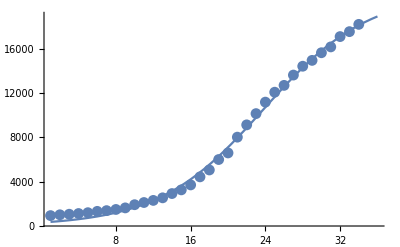

```mathematica
showplots[justdata,jdp0,justtime]
```

```mathematica
{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime]
```

{{21078.5,299.804,0.178029},1,7.86745×10^-8,34}

{20492.9,251.087,0.187313}

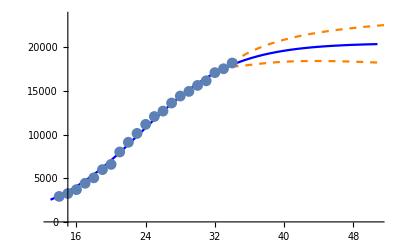
{-Graphics-,381.365,257.729,657,-10.5649,88.8355}

```mathematica
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,28,justtime,{1,0}];
jp20
jpdata20=justdata[[-21;;]];
datastats[jpdata20,jp20,1.8,2,justtime[[-21;;]]]
```

```mathematica
estimates[justdata,jdp0,28,justtime];
```

backward result : {25787.1,368.544,0.161986}

forward result : {20492.9,251.087,0.187313}

```mathematica
TableView[Transpose[generatestats[justdata,jdp0,28,justtime,jstartdate]]];
```

{981.19,4.49853,0.341492}

{1452.18,18.7219,0.227054}

{1452.18,18.7219,0.227054}

```mathematica
{"Russia",300,{133764.28972174952,345.7178233894532,0.17211220984196077},21,14,10,0}
```

```mathematica
{"Japan",950,{17986.663577976567,576.9474735585374,0.12382285884487645},21,14,8,0}
```

```mathematica
{name,trunc,cp0,lag,projt,bootl,drop}
```

```mathematica
{"Sweden",200,{23138.83457722449,461.922977379802,0.10293773671900139},28,14,10,0}
```

```mathematica
{"Spain",300,{215675.98160202175,3181.500137016704,0.14826151757050574},28,14,10,0}
```

```mathematica
{"Denmark",1100,{9249.181828199724,848.3550476707888,0.11809736637519559},28,14,10,0}
```

```mathematica
{"Greece",50,{2469.7252428688025,97.9216579531985,0.1381653045706424},21,14,10,0}
```

{Greece,50,{2469.73,97.9217,0.138165},21,14,10,0}

```mathematica
{"United Kingdom",200,{181106.79697173668,1069.9501757425367,0.1337539999625829},21,14,10,0}
{"Hungary",50,{3365.6444625267736,104.40659882066325,0.11408451894205024},28,14,10,0}
{"France",50,{177276.3912847858,1518.766119969371,0.13797898997605668},28,14,10,0}
{"Singapore",900,{21078.466173566427,299.80354836134035,0.17802870984146776},28,14,5,0}
```

backward result : {25787.1,368.544,0.161986}

forward result : {20492.9,251.087,0.187313}

last tab: {20492.9,251.087,0.187313}

backward result : {25787.1,368.544,0.161986}

forward result : {20492.9,251.087,0.187313}

past errors : {{-585.975,-827.447,-602.69,-798.856,-721.112},-707.216}

boot tab : {{18609.7,185.163,0.206979},{19843.4,225.079,0.194109}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34}

May 04

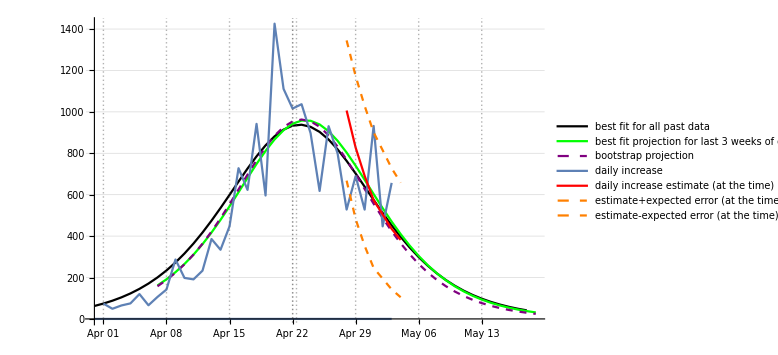

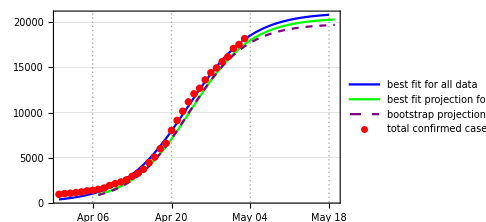

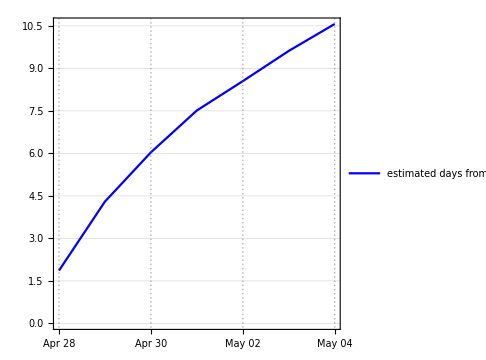

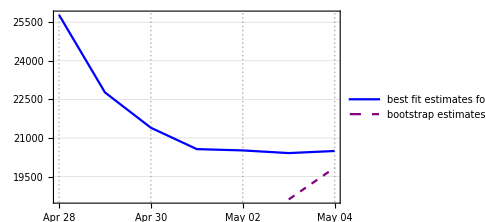

```mathematica
{jgraf,jloggraf,jdfpplot,jprogplot,jfinal,cboo}=somegraphs2[jdp0,jp20,justtime,justdata,jstartdate,28,14,0,5,1000];
jdatestring=reldatetostring[jstartdate,justtime[[-1]]]
jgraf
jloggraf
jdfpplot
jfinal
```